```mathematica
(* First we want to find the Basic Reproduction Number so that we can determine criterion to solve the numerical equations. We use the "next generation method" *)
```

```mathematica
V={{d+k, 0}, {-k, d+α}}
```

{{d+k,0},{-k,d+α}}

```mathematica
Vinv = Inverse[V]
```

{{1/(d+k),0},{k/((d+k) (d+α)),1/(d+α)}}

```mathematica
F = {{ϵ*β*S0, β*S0},{0,0}}
```

{{S0 β ϵ,S0 β},{0,0}}

```mathematica
F.Vinv
```

{{(k S0 β)/((d+k) (d+α))+(S0 β ϵ)/(d+k),(S0 β)/(d+α)},{0,0}}

```mathematica
(* Since this is an upper triangular matrix, the eigenvalues are on the diagonal. The spectral radius is therefore: (k S0 β)/((d+k) (d+α))+(S0 β ϵ)/(d+k) *)
```

```mathematica
(* We now want to find the numerical solutions. *)
```

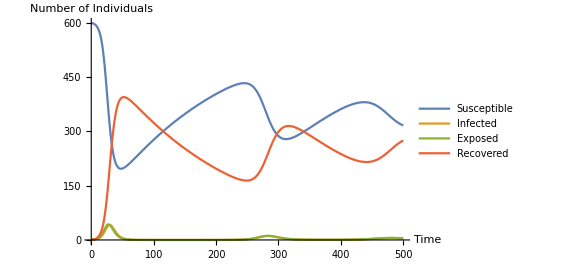

1.77041

```mathematica
equations = {
s'[t] == A - d*s[t] -β*s[t]*i[t] - ϵ*β*s[t]*e[t],
e'[t]==β*s[t]*i[t] + ϵ*β*s[t]*e[t] - (d+k)*e[t],
i'[t] == k*e[t] - (d+α)*i[t],
r'[t] == α*i[t] -d*r[t],
s[0]==A/d,e[0]==0, i[0]==1,r[0]==0
};
(* R0<1 is when beta 0.00056, 
R0>1 is when beta 0.00057 *)
params = {A->3, d->0.005,β->0.001,ϵ->0.5,k->1/2.0 ,α->1/2.0 };
totaltime = 500;
solutions = NDSolve[equations/.params,{s[t], e[t], i[t], r[t]},{t,0,totaltime}];
Plot[{Evaluate[s[t]/.solutions],Evaluate[i[t]/. solutions],Evaluate[e[t]/. solutions],Evaluate[r[t]/.solutions]}, {t,0,totaltime},PlotLegends->Placed[{"Susceptible", "Infected","Exposed", "Recovered"},{0.85,0.75}],AxesLabel->{"Time","Number of Individuals"},Axes->True]
R0 =((k *(A/d)* β)/((d+k) (d+α))+((A/d)*β ϵ)/(d+k))/.params
```